trial function: (∫_1)^10 dx x^2*e^-x

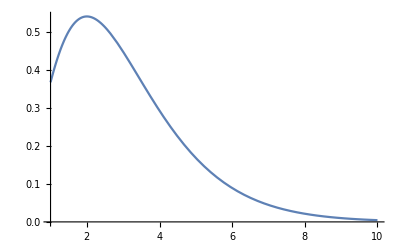

```mathematica
Plot[x^2 Exp[-x],{x,1,10}]
```

```mathematica
real=NIntegrate[x^2 Exp[-x],{x,1,10}]
```

1.83386

step:20	fdel=0.05
 Begin to test two integral algorithms
 Following is exponential integral algorithm
   1.83370516670564
 Following is trapezoid integral algorithm
   1.63556291487208

step:50 	fdel=0.02
 Begin to test two integral algorithms
 Following is exponential integral algorithm
   1.83383389257827
 Following is trapezoid integral algorithm
   1.76200099995380

step:100 	fdel=0.01
 Begin to test two integral algorithms
 Following is exponential integral algorithm
   1.83385228388523
 Following is trapezoid integral algorithm
   1.79947178091059

step:200 	fdel=0.005
 Begin to test two integral algorithms
 Following is exponential integral algorithm
   1.83385688178609
 Following is trapezoid integral algorithm
   1.81707785224022

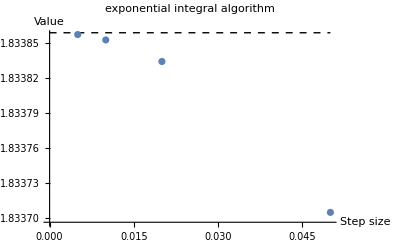

```mathematica
fdel={0.05,0.02,0.01,0.005};
exp={1.83370516670564,1.83383389257827,1.83385228388523,1.83385688178609};
trap={1.63556291487208,1.76200099995380,1.79947178091059,1.81707785224022};
ListPlot[{Table[{fdel[[i]],exp[[i]]},{i,1,4}](*,Table[{fdel[[i]],trap[[i]]},{i,1,4}]*)},Epilog->{Dashed,Line[{{0,real},{fdel[[1]],real}}]},AxesLabel->{"Step size","Value"},PlotLabel->"exponential integral algorithm"]
```

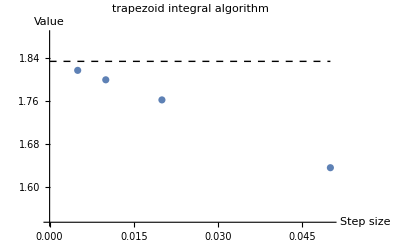

```mathematica
ListPlot[{Table[{fdel[[i]],trap[[i]]},{i,1,4}]},Epilog->{Dashed,Line[{{0,real},{fdel[[1]],real}}]},AxesLabel->{"Step size","Value"},PlotRange->{Automatic,{real-0.3,real+0.05}},PlotLabel->"trapezoid integral algorithm"]
```

trial function: (∫_0)^1 dx(∫_0)^((1-x)/2)dy(∫_0)^(1-x-2y)dz 10^4 xyz

```mathematica
f[x_,y_,z_]:=10^4*x*y*z;
x1=0;x2=1;
y1[x_]:=0;y2[x_]:=(1-x)/2;
z1[x_,y_]:=0;z2[x_,y_]:=1-x-2y;
```

```mathematica
real=NIntegrate[f[x,y,z],{x,x1,x2},{y,y1[x],y2[x]},{z,z1[x,y],z2[x,y]}]
```

3.47222

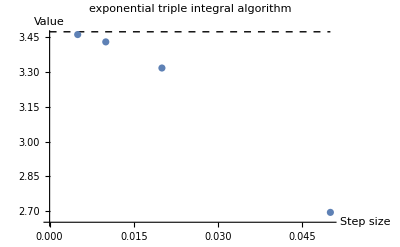

```mathematica
fdel={0.05,0.02,0.01,0.005};
exp={2.695022134660193,3.31633513816309,3.42875067299188,3.46035385315184};
ListPlot[{Table[{fdel[[i]],exp[[i]]},{i,1,4}]},Epilog->{Dashed,Line[{{0,real},{fdel[[1]],real}}]},AxesLabel->{"Step size","Value"},PlotLabel->"exponential triple integral algorithm"]
```

Begin to test triple integral convergence
 Following is exponential integral algorithm
 step:         20 , fdel:  5.000000000000000E-002
   2.69502213466019

Begin to test triple integral convergence
 Following is exponential integral algorithm
 step:          50 , fdel:  2.000000000000000E-002
   3.31633513816309

Begin to test triple integral convergence
 Following is exponential integral algorithm
 step:         100 , fdel:  1.000000000000000E-002
   3.42875067299188

Begin to test triple integral convergence
 Following is exponential integral algorithm
 step:         200 , fdel:  5.000000000000000E-003
   3.46035385315184